```mathematica
f[x_,y_,z_]:=x*(y*z-1)+(z*Log[2,1-2^-x])*(y-1)
```

```mathematica
f[x,y,z]
```

x (-1+y z)+((-1+y) z Log[1-2^-x])/Log[2]

```mathematica
Plot3D[f[x,y,10000],{x,1,32},{y,0,1}]
```

-Graphics3D-

```mathematica
g[a_]:=ArgMin[{f[x,a,1000],x>0},x]
```

```mathematica
g[.1]
```

3.33498

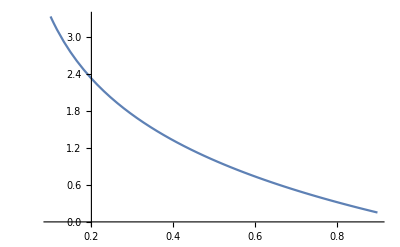

```mathematica
Plot[g[a],{a,0.1,.9}]
```

```mathematica
h[a_]:=Minimize[{f[x,a,1000],x>0},x]
```

```mathematica
h[.1][[1]]
```

465.667

```mathematica
Plot[h[a][[1]],{a,.2,.8},PlotPoints->10,MaxRecursion->0]
```